# Simulations

## Parameters

```mathematica
ClearAll[cg,Vg,R, δlac, mE,y, Nf, Nr];
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
```

## Functions

Polytope

```mathematica
ClearAll[vo,vl,vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal]
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;
vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

vgMinGlobal = 0;
vgMaxGlobal[ξ_] :=   Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(1+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];

vertexes[ξ_]:=If[vatpMaxGlobal[ξ]>Nr * R,
{{vatpMinGlobal,vgMinGlobal},{Nf * vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]},{(1 + Nr)R,R/Nf}},
{{vatpMinGlobal,vgMinGlobal},{Nf * vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]}}]
```

```mathematica
ClearAll[polytope,showPolytope];
polytope[ξ_][vg_,vatp_]:=Boole[vatpMinLocal[vg] ≤ vatp ≤ vatpMaxLocal[vg] ∧ vgMinLocal[vatp]≤vg≤vgMaxLocal[ξ][vatp]];
showPolytope[ξ_] := Module[{},
Show[
ListPlot[vertexes[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,0,vatpMaxGlobal[ξ]},{vg,0,vgMaxGlobal[ξ]}]]];
```

Growth Functions

```mathematica
ClearAll[δ,λ,λmax]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][vgMinGlobal,vatpMaxGlobal[ξ]]
```

Probability Distribution

```mathematica
ClearAll[distribution, showDistribution];

(* the distribution of the Probability inside the politope*)
distribution[ξ_,β_,vatp_] := Evaluate@Exp[-β y(vatpMaxGlobal[ξ]-vatp)];

(* Test *)
showDistribution[ξ_] := GraphicsGrid[
Table[
Table[
Plot[distribution[ξ,3^(c + 3r-3),vatp],{vatp,0,vatpMaxGlobal[ξ]}, PlotRange->All, PlotLabel->Style[ StringJoin["β value: ", ToString[3^(c + 3r-3)], "\nξ value: ",ToString[ξ]],10,Red]],
{c,1,3}
],
{r,1,3}
],
ImageSize->Scaled[.8]]
```

Integrals

```mathematica
totalIntegral[{vg,vatp}↦ vatp, β,ξ]
```

```mathematica
ClearAll[generalIntegral,totalIntegral, integrateOnlyForVg,integrateOnlyForVatp]
(* General Integral *) 
generalIntegral[fun_,β_,ξ_,{vatplb_,vatpub_},{glbf_,gubf_}]= Module[{int0,int1},
int1=Simplify@Integrate[distribution[ξ,β,vatp]fun[vg,vatp],
{vatp,vatplb,vatpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{vatplb,vatpub}∈Reals];
int0=Simplify@Integrate[fun[vg,vatp],{vatp,vatplb,vatpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{vatplb,vatpub}∈Reals];
Piecewise[{{0, vatplb≥vatpub}, {int1, β>0}, {int0, β==0}}]];

(* Total Integral *)
totalIntegral[fun_, β_,ξ_] = Simplify@Evaluate@generalIntegral[fun, β,ξ,{vatpMinGlobal,vatpMaxGlobal[ξ]},
{{ξ0,vatp} ↦ vgMinLocal[vatp],{ξ0,vatp}↦ vgMaxLocal[ξ][vatp]} ];
totalIntegral[β_,ξ_] = totalIntegral[{vg,vatp} ↦ 1,β,ξ];

(* Partial Integral for vg *)
integrateOnlyForVg[fun_,β_,ξ_, vatp0_] =Simplify@Evaluate@Integrate[distribution[ξ,β,vatp0]*fun[vg,vatp0],{vg,vgMinLocal[vatp0],vgMaxLocal[ξ][vatp0]}, Assumptions-> {vatp0,β,ξ} ∈Reals];
integrateOnlyForVg[β_,ξ_,vatp0_] = Simplify@Evaluate@integrateOnlyForVg[{vg,vatp} ↦ 1, β,ξ,vatp0];

(* Partial Integral for vatp *)
integrateOnlyForVatp[fun_,β_,ξ_, vg0_] = Simplify@Evaluate@Integrate[distribution[ξ,β,vatp]*fun[vg0,vatp],{vatp,vatpMinLocal[vg0],vatpMaxLocal[vg0]}, Assumptions-> {vg0,β,ξ} ∈Reals];
integrateOnlyForVatp[β_,ξ_, vg0_] =Simplify@Evaluate@integrateOnlyForVatp[{vg,vatp} ↦ 1 ,β,ξ, vg0] ;
```

Expected values

```mathematica
ClearAll[expZ,expVatp,expVg,expVl];
expZ[β_,ξ_] =Simplify@totalIntegral[β,ξ ];
```

```mathematica
expVatp[β_,ξ_] =Module[{ifNotInfinite},
ifNotInfinite[β_,ξ_] =  Evaluate[totalIntegral[{vg,vatp} ↦ vatp, β,ξ ]/expZ[β,ξ]];
If[β == ∞,Evaluate@vatpMaxGlobal[ξ], ifNotInfinite[β,ξ]]
];
```

```mathematica
expVg[β_,ξ_] = Module[{ifNotInfinite},
ifNotInfinite[β_,ξ_] =  Evaluate[totalIntegral[{vg,vatp} ↦ vg, β,ξ ]/expZ[β,ξ]];If[β == ∞,Evaluate@vgMaxGlobal[ξ] ,  ifNotInfinite[β,ξ]]
];
```

```mathematica
expVl[β_,ξ_] = Simplify@(expVatp[β,ξ] - expVg[β,ξ] * Nf*(1+ Nr))/Nr;
expV0[β_,ξ_] = Simplify@Min[ Nf * expVg[β,ξ],R];
```

Variances and covariances

```mathematica
ClearAll[pVatp,pVg,pVgVatp]
(* Probability associated with a given vatp value *)
pVatp[β_,ξ_,vatp0_] := Simplify@Evaluate@integrateOnlyForVg[ β,ξ, vatp0]/totalIntegral[β,ξ];

(* Probability associated with a given vg value *)
pVg[β_,ξ_,vg0_] :=Simplify@Evaluate@integrateOnlyForVatp[β,ξ,vg0]/totalIntegral[β,ξ];

(* Probability associated with a given vatp ang vg value *)
pVgVatp[β_,ξ_,vatp0_,vg0_] := Simplify@Evaluate@If[vgMinLocal[vatp0] ≤ vg0 ≤ vgMaxLocal[ξ][vatp0],
pVatp[β,ξ,vatp0]/(vgMaxLocal[ξ][vatp0] - vgMinLocal[vatp0]),
0
];
```

Equilibrium (Chemostat)

```mathematica
ClearAll[sgEq, slEq, DEq, XEq];
sgEq[β_,ξ_] := Simplify@Evaluate[cg - ξ * expVg[β,ξ]];
slEq[β_,ξ_] := Simplify@Evaluate[- ξ expVl[β,ξ]];
DEq[β_,ξ_] := Simplify@Evaluate@λ[sgEq[β,ξ],slEq[β,ξ]][expVg[β,ξ],expVatp[β,ξ]];
XEq[β_,ξ_] := Simplify@Evaluate@DEq[β,ξ]ξ;
```

Graphics

Precalculation

ξunit: 0.0462963

βlist: {0,199.,1990.,∞}

ξmax: {1.29928,5.81736,15.2891,27.7778}

ξrange: {-3,0.251543}

Test

Total tests

Parameters:

Glucose in feed (cg): 15.

Universal max glc uptake (Vg): 0.5

Universal max respiration (R): 0.4

Date rate doto lactate (δlac): 0.0011

Maintenance ATP demand (mE): 1.

Units of atp needed to produce a unit of biomass (y): 0.00409938

Stoichiometric coeficient of fermentation (Nf): 2.

Stoichiometric coeficient of respiration (Nr): 19.

Number of maintained cells per unit of fresh culture per unit of time (ξ): 2.

"Heterogenity coeficient" (β): 2.

Polytope:

Global min vatp value (vatpMinGlobal): 0.

Global max vatp value (vatpMaxGlobal[ξ_]): 8.6

Local min vatp value (vatpMinLocal[vg_]) at vgMaxGlobal/2: 0.5

Local max vatp value (vatpMaxLocal[vg_]) at vgMaxGlobal/2: 8.1

Global min vg value (vgMinGlobal): 0.

Global max vg value (vgMaxGlobal[ξ_]): 0.5

Local min vg value (vgMinLocal[vatp_]) at vatpMaxGlobal/2: 0.1075

Local max vg value (vgMaxLocal[ξ_][vatp_]) at vatpMaxGlobal/2: 0.5

Polytope vertexes (vertexes[ξ_]): {{0.,0.},{1.,0.5},{8.6,0.5},{8.,0.2}}

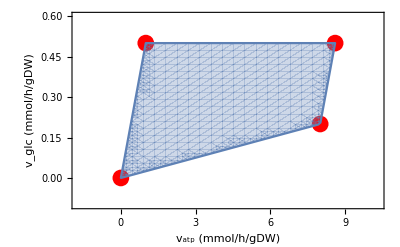

Probability Distribution:

Pribability distribution (Exp[-β y(vatpMaxGlobal[ξ]-vatp)])

Evaluated at vatpMaxGlobal/2: 0.96536

If Increase β decrease heterogeneity

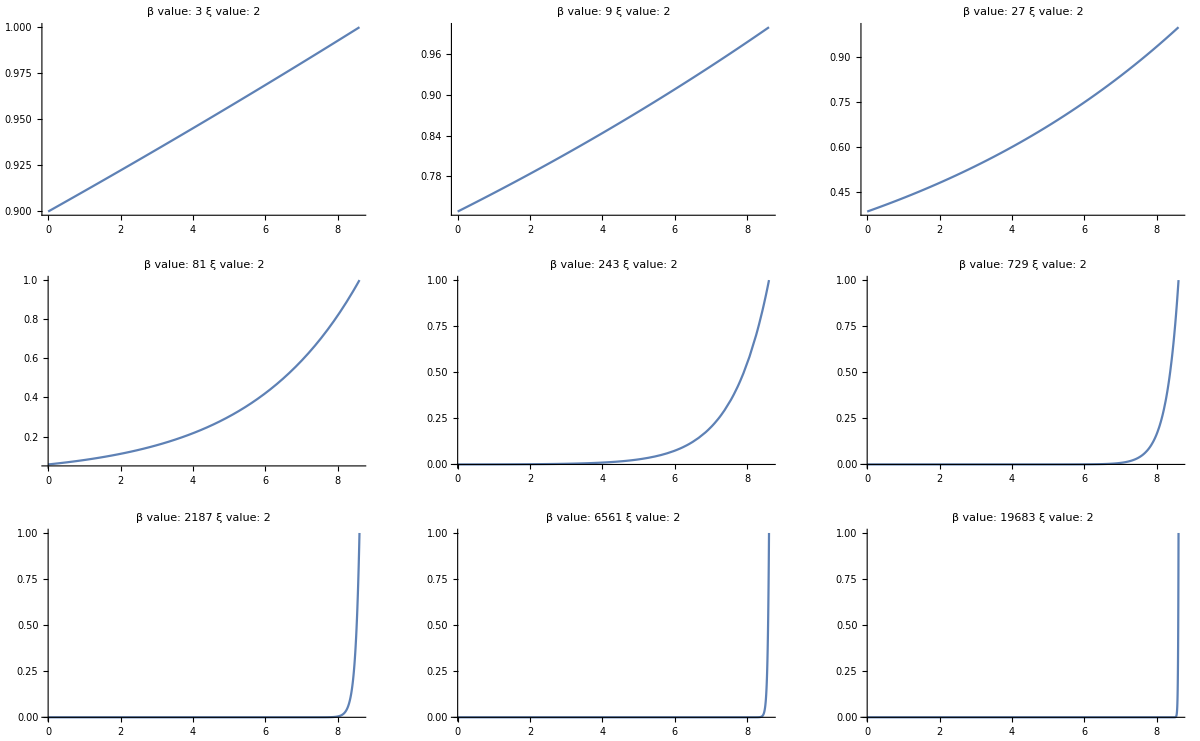

Integrals:

Integral over the polytope (generalIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]):

Total value: 2.92978

Integrate only for vg at vatp = vatpMaxGlobal/2: 0.378904

Integrate only for vapt at vg = vgMaxGlobal/2: 7.33792

Expected values:

Expected Z: 2.92978

Infinity::indet: Indeterminate expression 19+-∞+-∞+∞ encountered.

Expected Z at β = ∞: Indeterminate

Expected vatp: 4.11622

Expected vatp at β ∞: 8.6

Expected vg: 0.296587

Expected vg at β = ∞: 0.5

Expected vl: -0.40775

Expected vl at β = ∞: -0.6

Expected v0: 0.4

Expected v0 at ∞: 0.4

Probabilities:

Probability associated with vatp = vatpMaxGlobal/2: 0.129328

Probability associated with vg = vgMaxGlobal/2: 2.5046

Probability associated* with vg = vgMaxGlobal/2 and 
vatp = vatpMaxGlobal/2: 0.329499

Equilibrium (Chemostat):

Substrate concentration: 14.4068

Waste concentration: 0.815501

Dilution Rate (D): 0.0118775

Cell density (X): 0.0237551

```mathematica
(* Test *)
Module [{ξ,β},
ξ = 2;
β = 2;
Print[Style["Total tests", 35]];
Print[Style["Parameters: ", 20, Red]];
Print["Glucose in feed (cg): ", cg//N];
Print["Universal max glc uptake (Vg): ", Vg//N];
Print["Universal max respiration (R): ", R//N];
Print["Date rate doto lactate (δlac): ", δlac//N];
Print["Maintenance ATP demand (mE): ", mE//N];
Print["Units of atp needed to produce a unit of biomass (y): ", y//N];
Print["Stoichiometric coeficient of fermentation (Nf): ", Nf//N];
Print["Stoichiometric coeficient of respiration (Nr): ", Nr//N];
Print["Number of maintained cells per unit of fresh culture per unit of time (ξ): ", ξ//N];
Print["\"Heterogenity coeficient\" (β): ", β//N];
Print[""];

Print[Style["Polytope: ", 20, Red]];
Print["Global min vatp value (vatpMinGlobal): ", vatpMinGlobal//N];
Print["Global max vatp value (vatpMaxGlobal[ξ_]): ", vatpMaxGlobal[ξ]//N];
Print["Local min vatp value (vatpMinLocal[vg_]) at vgMaxGlobal/2: ", vatpMinLocal[vgMaxGlobal[ξ]/2]//N];
Print["Local max vatp value (vatpMaxLocal[vg_]) at vgMaxGlobal/2: ", vatpMaxLocal[vgMaxGlobal[ξ]/2]//N];
Print["Global min vg value (vgMinGlobal): ", vgMinGlobal//N];

Print["Global max vg value (vgMaxGlobal[ξ_]): ", vgMaxGlobal[ξ]//N];
Print["Local min vg value (vgMinLocal[vatp_]) at vatpMaxGlobal/2: ", vgMinLocal[vatpMaxGlobal[ξ]/2]//N];
Print["Local max vg value (vgMaxLocal[ξ_][vatp_]) at vatpMaxGlobal/2: ", vgMaxLocal[ξ][vatpMaxGlobal[ξ]/2]//N];
Print["Polytope vertexes (vertexes[ξ_]): ", vertexes[ξ]//N];
Print[showPolytope[2]];
Print[""];

Print[Style["Probability Distribution:", 20, Red]];
Print["Pribability distribution (Exp[-β y(vatpMaxGlobal[ξ]-vatp)])"];
Print["Evaluated at vatpMaxGlobal/2: ", distribution[ξ,β,vatpMaxGlobal[ξ]/2]//N];
Print["If Increase β decrease heterogeneity"];
Print[showDistribution[ξ]];

Print[""];
Print[Style["Integrals: ", 20, Red]];
Print["Integral over the polytope (generalIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]):"];
Print["Total value: ", totalIntegral[ξ,β]//N];
Print["Integrate only for vg at vatp = vatpMaxGlobal/2: ", integrateOnlyForVg[β,ξ, vatpMaxGlobal[ξ]/2]//N];
Print["Integrate only for vapt at vg = vgMaxGlobal/2: ", integrateOnlyForVatp[β,ξ, vgMaxGlobal[ξ]/2]//N];

Print[""];
Print[Style["Expected values: ", 20, Red]];
Print["Expected Z: ",expZ[β,ξ]//N];
Print["Expected Z at β = ∞: ",expZ[∞,ξ]//N];
Print["Expected vatp: ",expVatp[β,ξ]//N];
Print["Expected vatp at β ∞: ",expVatp[∞,ξ]//N];
Print["Expected vg: ", expVg[β,ξ]//N];
Print["Expected vg at β = ∞: ", expVg[∞,ξ]//N];
Print["Expected vl: ",  expVl[β,ξ]//N];
Print["Expected vl at β = ∞: ",  expVl[∞,ξ]//N];
Print["Expected v0: ",  expV0[β,ξ]//N];
Print["Expected v0 at ∞: ",  expV0[∞,ξ]//N];

Print[""];
Print[Style["Probabilities: ", 20, Red]];
Print["Probability associated with vatp = vatpMaxGlobal/2: ",
pVatp[β,ξ,vatpMaxGlobal[ξ]/2]//N];
Print["Probability associated with vg = vgMaxGlobal/2: ",
pVg[β,ξ,vgMaxGlobal[ξ]/2]//N];
Print["Probability associated* with vg = vgMaxGlobal/2 and 
vatp = vatpMaxGlobal/2: ",
pVgVatp[β,ξ,vatpMaxGlobal[ξ]/2,vgMaxGlobal[ξ]/2]//N];


Print[""];
Print[Style["Equilibrium (Chemostat): ", 20, Red]];
Print["Substrate concentration: ", sgEq[β,ξ]//N];
Print["Waste concentration: ", slEq[β,ξ]//N];
Print["Dilution Rate (D): ", DEq[β,ξ]//N];
Print["Cell density (X): ", XEq[β,ξ]//N];
]
```